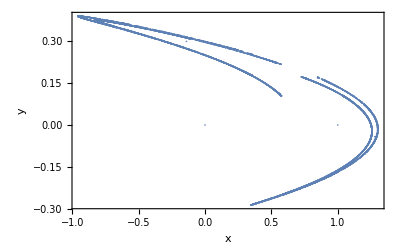

```mathematica
y = 0;
t = 0;
out = {{0, 0}};
For[ii = 1, ii<10000, ii++, 
x = y + 1 - 1.14*t^2;
y = 0.3 * t;
res = {{x, y}};
t = x;
outt = Join[out, res];
out = outt;
]
ListPlot[out, Frame-> True, PlotRange->All, FrameStyle->Thick, FrameLabel->{"x", "y"}, PlotStyle->Thick]
```

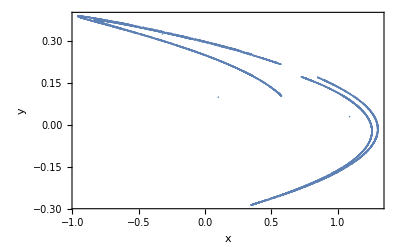

```mathematica
y = 0.1;
t = 0.1;
out = {{0.1, 0.1}};
For[ii = 1, ii<10000, ii++, 
x = y + 1 - 1.14*t^2;
y = 0.3 * t;
res = {{x, y}};
t = x;
outt = Join[out, res];
out = outt;
]
ListPlot[out, Frame-> True, PlotRange->All, FrameStyle->Thick, FrameLabel->{"x", "y"}, PlotStyle->Thick]
```